22

22

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

Schw3-1c.xls

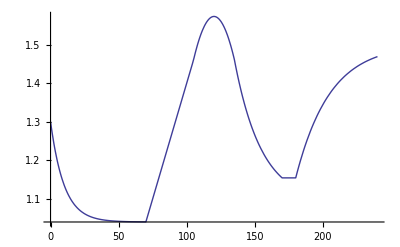

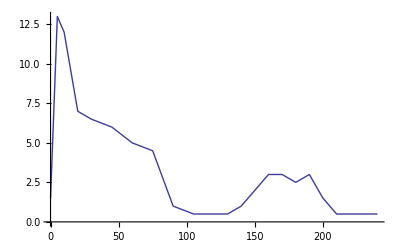

3

```mathematica
(*p1*)
texpLong={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
Length[%]
texp=Take[texpLong,11];
PexpPmolLong={1.5,13,12,7,6.5,6,5,4.5,1,.5,.5,.5,1,2,3,3,2.5,3,1.5,.5,.5,.5};
Length[%]
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol;
ca0=1.3;
sc=NDSolve[{Ca'[t]==Piecewise[{{0.1*(1.04-Ca[t]),t<70},{.06/5,70≤t<105},{0.001*(120-t),105≤t<135},{0.05*(1.09-Ca[t]),135≤t<170},{0,170≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,240,2.5}];
Export["Schw3-1c.xls",%]
Show[Plot[Evaluate[Ca[t]/.sc],{t,0,240},PlotRange->All]]
ListPlot[Transpose[{texpLong,PexpPmolLong}],Joined->True]
SVol=3
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.1*(1.04-Ca[t]),t<70},{.06/5,70≤t<105},{0.001*(120-t),105≤t<135},{0.05*(1.09-Ca[t]),135≤t<170},{0,170≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,240}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.36173×10^-10, 3.25005, 1.11859×10^-10}, is returned.

{36565.1,{kv→30.0032,a→0.001,b→5.86338×10^-13,beta→0.30564,gamma→0.30564,kd→1.14936,m→20.1908}}

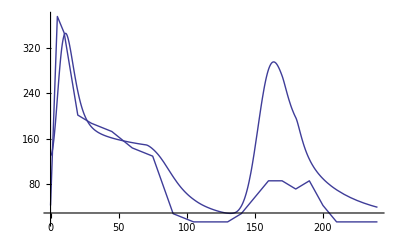

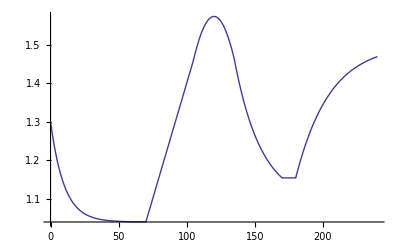

Schw3-1a.xls

Schw3-1b.xls

36565.2

0.766357

0.376073

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
kvex=30.0032;
aa=0.001;
bb=.00000005;
bet=.30564;
gam=.30564;
kd=1.14936;
m=20.1908;
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.1*(1.04-Ca[t]),t<70},{.06/5,70≤t<105},{0.001*(120-t),105≤t<135},{0.05*(1.09-Ca[t]),135≤t<170},{0,170≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Show[Plot[Evaluate[P[t]/.s],{t,0,240},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]
Plot[Evaluate[Ca[t]/.s],{t,0,240},PlotRange->All]

T2=Table[{t,P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,240},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-1b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

22

22

{57.6,345.6,403.2,259.2,201.6,201.6,172.8,115.2,43.2,28.8,14.4}

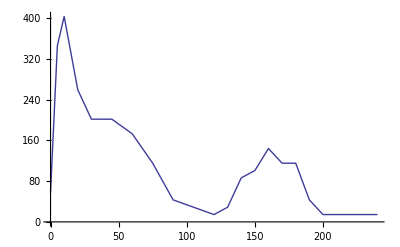

1.25

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

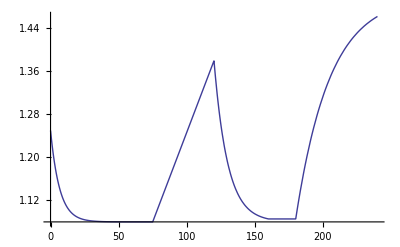

Schw3-2c.xls

3

```mathematica
(*p2*)
texpLong={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
Length[%]
texp=Take[texpLong,11];
PexpPmolLong={2,12,14,9,7,7,6,4,1.5,1,.5,1,3,3.5,5,4,4,1.5,.5,.5,.5,.5};
Length[%]
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.25
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{0.1*(1.08-Ca[t]),120≤t<160},{0,160≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,240},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,240,2.5}];
Export["Schw3-2c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
SVol=3
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{0.1*(1.08-Ca[t]),120≤t<160},{0,160≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,240}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {6.32808×10^-11, 0.37978, 2.08958×10^-11}, is returned.

{35376.1,{kv→30.1181,a→0.001,b→5.86338×10^-13,beta→0.271778,gamma→0.271778,kd→1.09154,m→20.1339}}

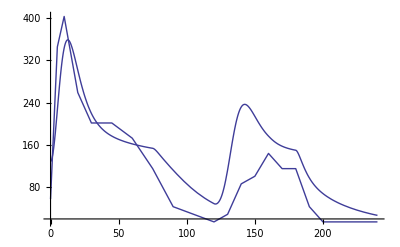

Schw3-2a.xls

Schw3-2b.xls

35376.1

0.793095

0.654959

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];

bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{0.1*(1.08-Ca[t]),120≤t<160},{0,160≤t<180},{0.04*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Show[Plot[Evaluate[P[t]/.s],{t,0,240},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]

T2=Table[{t,P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-2a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,240},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-2b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

22

22

{28.8,489.6,432.,230.4,129.6,115.2,115.2,28.8,7.2,7.2,7.2}

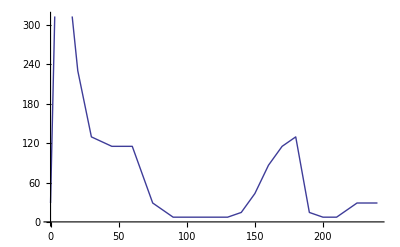

1.3

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

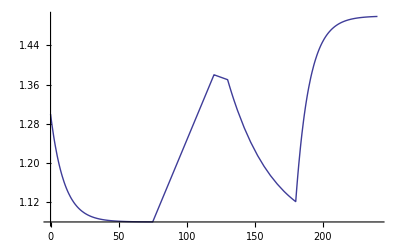

Schw3-3c.xls

```mathematica
(*p3*)
texpLong={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
Length[%]
texp=Take[texpLong,11];
PexpPmolLong={1,17,15,8,4.5,4,4,1,.25,.25,.25,.25,.5,1.5,3,4,4.5,.5,.25,.25,1,1};
Length[%]
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.3
sc=NDSolve[{Ca'[t]==Piecewise[{{0.1*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{-0.001,120≤t<130},{0.03*(1.05-Ca[t]),130≤t<180},{0.1*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,240},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,240,2.5}];
Export["Schw3-3c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.1*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{-0.001,120≤t<130},{0.03*(1.05-Ca[t]),130≤t<180},{0.1*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,240}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.0813×10^-10, 0.846541, 3.58463×10^-11}, is returned.

{150219.,{kv→29.9428,a→0.001,b→5.86338×10^-13,beta→0.287856,gamma→0.287856,kd→1.145,m→20.0793}}

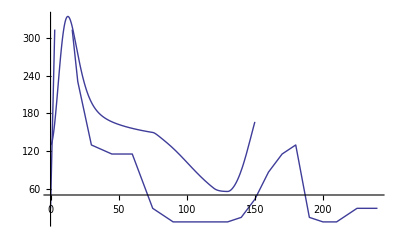

Schw3-3a.xls

Schw3-3b.xls

150219.

0.489736

0.4297

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
Ca'[t]==Piecewise[{{0.1*(1.08-Ca[t]),t<75},{.04/6,75≤t<120},{-0.001,120≤t<130},{0.03*(1.05-Ca[t]),130≤t<180},{0.1*(1.5-Ca[t]),180≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-3a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,240},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-3b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

22

22

{57.6,576.,590.4,432.,316.8,201.6,187.2,201.6,43.2,28.8,14.4}

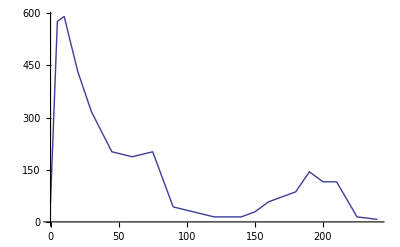

1.25

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

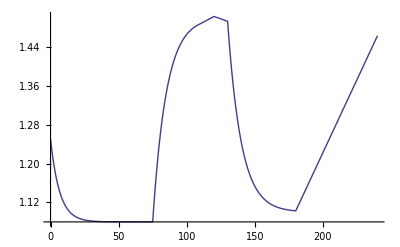

Schw3-4c.xls

```mathematica
(*p4*)
texpLong={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
Length[%]
texp=Take[texpLong,11];
PexpPmolLong={2,20,20.5,15,11,7,6.5,7,1.5,1,.5,.5,.5,1,2,2.5,3,5,4,4,.5,.25};
Length[%]
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.25
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{0.1*(1.5-Ca[t]),75<=t<110},{.0015,110≤t<120},{-0.001,120≤t<130},{0.1*(1.1-Ca[t]),130≤t<180},{0.006,180≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,240},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,240,2.5}];
Export["Schw3-4c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{0.1*(1.5-Ca[t]),75<=t<110},{.0015,110≤t<120},{-0.001,120≤t<130},{0.1*(1.1-Ca[t]),130≤t<180},{0.006,180≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,240}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.40385×10^-11, 0.00850102, 4.48644×10^-12}, is returned.

{27689.1,{kv→37.6202,a→0.001,b→2.25367×10^-12,beta→0.143991,gamma→0.143991,kd→1.18177,m→43.2608}}

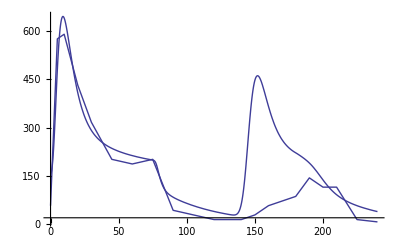

Schw3-4a.xls

Schw3-4b.xls

27689.1

0.938696

0.447929

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{0.1*(1.5-Ca[t]),75<=t<110},{.0015,110≤t<120},{-0.001,120≤t<130},{0.1*(1.1-Ca[t]),130≤t<180},{0.006,180≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Show[Plot[Evaluate[P[t]/.s],{t,0,240},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-4a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,240},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-4b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

22

22

{28.8,345.6,403.2,489.6,345.6,316.8,201.6,187.2,57.6,28.8,7.2}

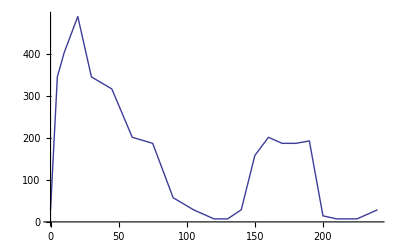

1.22

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

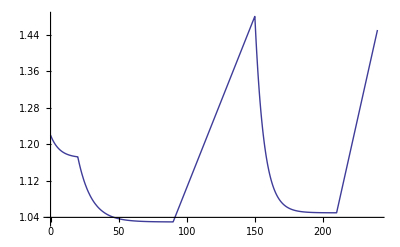

Schw3-5c.xls

```mathematica
(*p5*)
texpLong={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
Length[%]
texp=Take[texpLong,11];
PexpPmolLong={1,12,14,17,12,11,7,6.5,2,1,.25,.25,1,5.5,7,6.5,6.5,6.7,.5,.25,.25,1};
Length[%]
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.22
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.17-Ca[t]),t<20},{0.1*(1.03-Ca[t]),20<=t<90},{.045/6,90≤t<150},{0.15*(1.05-Ca[t]),150≤t<210},{.08/6,210≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,240},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,240,2.5}];
Export["Schw3-5c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{0.1*(1.5-Ca[t]),75<=t<110},{.0015,110≤t<120},{-0.001,120≤t<130},{0.1*(1.1-Ca[t]),130≤t<180},{0.006,180≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,240}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.73681×10^-10, 0.0693167, 5.76938×10^-11}, is returned.

{37107.5,{kv→30.3667,a→0.001,b→5.86338×10^-13,beta→0.209704,gamma→0.209704,kd→1.04191,m→21.3674}}

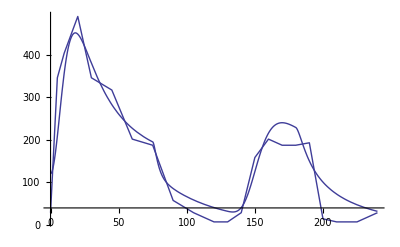

Schw3-5a.xls

Schw3-5b.xls

37107.5

0.873504

0.872508

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];

s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
Ca'[t]==Piecewise[{{0.15*(1.08-Ca[t]),t<75},{0.1*(1.5-Ca[t]),75<=t<110},{.0015,110≤t<120},{-0.001,120≤t<130},{0.1*(1.1-Ca[t]),130≤t<180},{0.006,180≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Show[Plot[Evaluate[P[t]/.s],{t,0,240},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-5a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,240,2.5}];
Export["Schw3-5b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```